```mathematica
(* Fits to log stable below. Starting with 90d worth of data from WETH/USDC .... *)
```

```mathematica
(* Import from csv *)
```

```mathematica
Directory[]
```

/Users/personal

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/personal/Desktop/note7/points

```mathematica
(* Go back and download WETH/USDC data from cron. Look at that *)
```

```mathematica
tblWethUsdc90d = Import["90/data-1625069716_weth-usdc-twap.csv"]
```

{{,timestamp,twap},{0,1.61878×10^9,2.23957×10^9},{1,1.61878×10^9,2.24054×10^9},{2,1.61878×10^9,2.23817×10^9},{3,1.61878×10^9,2.25083×10^9},{4,1.61878×10^9,2.25656×10^9},{5,1.61878×10^9,2.25775×10^9},{6,1.61878×10^9,2.25804×10^9},9164,{9173,1.62507×10^9,2.13479×10^9},{9174,1.62507×10^9,2.12846×10^9},{9175,1.62507×10^9,2.1222×10^9},{9176,1.62507×10^9,2.11587×10^9},{9177,1.62507×10^9,2.11137×10^9},{9178,1.62507×10^9,2.10661×10^9},{9179,1.62507×10^9,2.10415×10^9}}
 |  |  |  |

```mathematica
Length[tblWethUsdc90d]
```

9179

```mathematica
FromUnixTime[tblWethUsdc90d[[2]][[2]]]
```

Sun 18 Apr 2021 16:50:52GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[tblWethUsdc90d]]][[2]]]
```

Wed 30 Jun 2021 12:09:58GMT-4.

```mathematica
twapsWethUsdc90d = Table[tblWethUsdc90d[[i]][[3]], {i, 2, Length[tblWethUsdc90d]}]
```

{2.23957×10^9,2.24054×10^9,2.23817×10^9,2.25083×10^9,2.25656×10^9,2.25775×10^9,2.25804×10^9,2.257×10^9,2.25322×10^9,1.74585×10^9,1.74538×10^9,1.74413×10^9,1.74262×10^9,1.74205×10^9,2.12343×10^9,2.12508×10^9,2.12091×10^9,2.11964×10^9,2.1185×10^9,2.11908×10^9,2.12379×10^9,2.13378×10^9,2.1414×10^9,2.14916×10^9,2.15618×10^9,2.1627×10^9,2.16623×10^9,2.1675×10^9,2.16946×10^9,1.33059×10^10,1.52229×10^10,2.17316×10^9,2.17288×10^9,2.17448×10^9,2.18326×10^9,2.18968×10^9,2.19585×10^9,2.20047×10^9,2.20447×10^9,2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9}

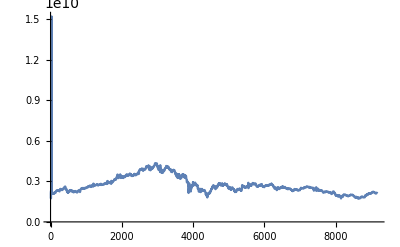

```mathematica
ListLinePlot[twapsWethUsdc90d, PlotRange->All]
```

```mathematica
(* Same issues here for early data as UNI/WETH. Cut off first 40 elements *)
twapsWethUsdc90dFiltered = Table[twapsWethUsdc90d[[i]], {i, 40, Length[twapsWethUsdc90d]}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9}

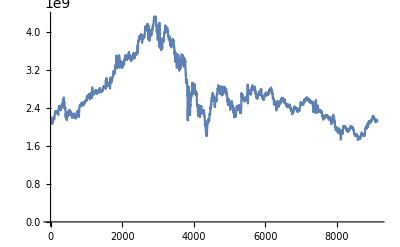

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered, PlotRange->All]
```

```mathematica
FromUnixTime[tblWethUsdc90d[[40]][[2]]]
```

Mon 19 Apr 2021 17:14:44GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[twapsWethUsdc90dFiltered]]][[2]]]
```

Wed 30 Jun 2021 04:33:51GMT-4.

```mathematica
(* Calculate the rs ... *)
```

```mathematica
rsWethUsdc90dFiltered = Differences[Log[twapsWethUsdc90dFiltered]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,9115,0.00150055,0.000591025,0.000421125,-0.000241228,-0.000868266,-0.00297129,-0.00294238,-0.00298715,-0.00213101,-0.00225849,-0.00116666}
 |  |  |  |

```mathematica
rsWethUsdc90dFiltered[[100]]
```

-0.00443888

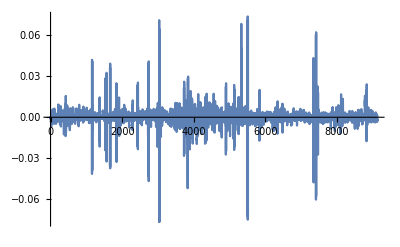

```mathematica
ListLinePlot[rsWethUsdc90dFiltered, PlotRange->All]
```

```mathematica
Length[rsWethUsdc90dFiltered]
```

9138

```mathematica
edistWethUsdc90dFiltered = EstimatedDistribution[rsWethUsdc90dFiltered, StableDistribution[1, aWU90d, bWU90d, locWU90d, scaleWU90d]]
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
(* This seems more reasonable. more data from weth/usdc lead to decrease in alpha because included massive run up to $4k *)
```

```mathematica
FromUnixTime[tblWethUsdc90d[[5000]][[2]]]
```

Fri 28 May 2021 06:16:07GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[tblWethUsdc90d]]][[2]]]
```

Wed 30 Jun 2021 12:09:58GMT-4.

```mathematica
(* Seems a good place to estimate k values would be 1h candles (from note-7.nb) *)
```

```mathematica
(* Some concrete numbers below in terms of funding rate ... *)
```

```mathematica
(* What does e^{mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)} translate to for ETH/USDC fit? *)
```

```mathematica
(* And if d = f * e^{mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)}, what f value should we use across the board to get k max interest rates on order of 1-10% daily? *)
```

```mathematica
(* e.x. d = 1.0014649 for T=10m results in 10% per day funding rate *)
```

```mathematica
edistWethUsdc90dFiltered
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
InverseCDF[edistWethUsdc90dFiltered, 0.99]
```

0.0124991

```mathematica
InverseCDF[edistWethUsdc90dFiltered, 0.95]
```

0.00479452

```mathematica
InverseCDF[edistWethUsdc90dFiltered, 0.90]
```

0.0032239

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered, 0.95]]
```

1.00481

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered, 0.99]]
```

1.01258

```mathematica
(* Produce 1 hour candles from 10min cron data to use in k analysis ... *)
```

```mathematica
twapsWethUsdc90dFiltered1HourCandle = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 6}]
```

{2.20799×10^9,2.20513×10^9,2.18452×10^9,2.13229×10^9,2.11006×10^9,2.07922×10^9,2.09635×10^9,2.12707×10^9,2.12948×10^9,2.08876×10^9,2.092×10^9,2.14019×10^9,2.15282×10^9,2.18679×10^9,2.18398×10^9,2.19238×10^9,2.20923×10^9,2.16313×10^9,2.2252×10^9,2.2656×10^9,2.28598×10^9,2.31448×10^9,2.31787×10^9,2.33849×10^9,2.327×10^9,2.34079×10^9,2.30593×10^9,2.31917×10^9,2.31566×10^9,2.29969×10^9,2.30039×10^9,2.31432×10^9,2.2911×10^9,2.29267×10^9,2.29931×10^9,2.26585×10^9,2.28924×10^9,2.36951×10^9,2.38804×10^9,2.43288×10^9,2.44522×10^9,2.42349×10^9,2.41306×10^9,2.43004×10^9,2.39108×10^9,2.38836×10^9,2.35824×10^9,2.35909×10^9,2.43401×10^9,2.38868×10^9,2.40558×10^9,2.43149×10^9,2.45836×10^9,2.47252×10^9,2.45963×10^9,2.44538×10^9,2.48836×10^9,2.53708×10^9,2.57431×10^9,2.56804×10^9,2.58211×10^9,2.59943×10^9,2.60893×10^9,2.54473×10^9,2.5154×10^9,2.45851×10^9,2.39695×10^9,2.4136×10^9,2.41881×10^9,2.39325×10^9,2.28152×10^9,2.24012×10^9,2.25792×10^9,2.20518×10^9,2.19372×10^9,2.1814×10^9,2.17754×10^9,2.20198×10^9,2.27401×10^9,2.28949×10^9,2.24668×10^9,2.25694×10^9,2.28855×10^9,2.33238×10^9,2.30586×10^9,2.34455×10^9,2.35986×10^9,2.34445×10^9,2.31699×10^9,2.33811×10^9,2.31129×10^9,2.27699×10^9,2.27259×10^9,2.30824×10^9,2.31167×10^9,2.31729×10^9,2.28115×10^9,2.2841×10^9,2.27321×10^9,2.2328×10^9,2.19895×10^9,2.21535×10^9,2.22182×10^9,2.20086×10^9,2.24249×10^9,2.23852×10^9,2.26192×10^9,2.2762×10^9,2.27615×10^9,2.28902×10^9,2.2637×10^9,2.23579×10^9,2.2202×10^9,2.2419×10^9,2.23764×10^9,2.19271×10^9,2.19508×10^9,2.20039×10^9,2.18244×10^9,2.20087×10^9,2.22228×10^9,2.27257×10^9,2.27791×10^9,2.31112×10^9,2.31413×10^9,2.33998×10^9,2.34076×10^9,2.34044×10^9,2.31663×10^9,2.29939×10^9,2.27635×10^9,2.21107×10^9,2.2594×10^9,2.2981×10^9,2.40696×10^9,2.44476×10^9,2.44623×10^9,2.45812×10^9,2.45375×10^9,2.47045×10^9,2.46507×10^9,2.44595×10^9,2.44323×10^9,2.48714×10^9,2.51503×10^9,2.50391×10^9,2.4989×10^9,2.48799×10^9,2.48933×10^9,2.50791×10^9,2.50156×10^9,2.49079×10^9,2.46433×10^9,2.4924×10^9,2.51696×10^9,2.52264×10^9,2.51242×10^9,2.52143×10^9,2.50823×10^9,2.49901×10^9,2.52488×10^9,2.55421×10^9,2.55383×10^9,2.54832×10^9,2.55165×10^9,2.55059×10^9,2.57182×10^9,2.5636×10^9,2.56814×10^9,2.6356×10^9,2.65748×10^9,2.63922×10^9,2.63722×10^9,2.62427×10^9,2.63619×10^9,2.63813×10^9,2.62802×10^9,2.67884×10^9,2.69579×10^9,2.68116×10^9,2.63928×10^9,2.63913×10^9,2.6043×10^9,2.5975×10^9,2.61809×10^9,2.6001×10^9,2.62146×10^9,2.68377×10^9,2.71902×10^9,2.69857×10^9,2.70519×10^9,2.68906×10^9,2.71774×10^9,2.72826×10^9,2.83875×10^9,2.71326×10^9,2.73414×10^9,2.72313×10^9,2.73961×10^9,2.72686×10^9,2.71973×10^9,2.71625×10^9,2.68881×10^9,2.69883×10^9,2.72397×10^9,2.73126×10^9,2.71824×10^9,2.7641×10^9,2.76668×10^9,2.76721×10^9,2.78625×10^9,2.76346×10^9,2.77752×10^9,2.76555×10^9,2.73519×10^9,2.71615×10^9,2.72296×10^9,2.70927×10^9,2.73315×10^9,2.76143×10^9,2.75368×10^9,2.73823×10^9,2.74219×10^9,2.74109×10^9,2.75674×10^9,2.76461×10^9,2.78123×10^9,2.77746×10^9,2.78216×10^9,2.76798×10^9,2.76317×10^9,2.74392×10^9,2.74595×10^9,2.75331×10^9,2.7459×10^9,2.75239×10^9,2.76471×10^9,2.76529×10^9,2.77799×10^9,2.7649×10^9,2.75652×10^9,2.7536×10^9,2.77048×10^9,2.76768×10^9,2.82967×10^9,2.83731×10^9,2.84274×10^9,2.86233×10^9,2.85625×10^9,2.85615×10^9,2.83934×10^9,2.83687×10^9,2.84947×10^9,2.86716×10^9,2.86996×10^9,2.86603×10^9,2.85328×10^9,2.88817×10^9,2.92512×10^9,2.93337×10^9,2.92361×10^9,2.93804×10^9,2.93166×10^9,2.94373×10^9,2.93936×10^9,2.93709×10^9,2.95137×10^9,2.91281×10^9,2.91731×10^9,2.91803×10^9,2.89507×10^9,2.87316×10^9,2.88564×10^9,2.91581×10^9,2.9211×10^9,2.92583×10^9,2.9166×10^9,2.81586×10^9,2.93313×10^9,2.93473×10^9,2.94487×10^9,2.97281×10^9,2.96885×10^9,2.97396×10^9,2.94192×10^9,2.96718×10^9,2.99205×10^9,3.01749×10^9,3.03939×10^9,3.0537×10^9,3.08027×10^9,3.09069×10^9,3.13349×10^9,3.17874×10^9,3.16742×10^9,3.14946×10^9,3.16459×10^9,3.13545×10^9,3.11962×10^9,3.17054×10^9,3.17997×10^9,3.26847×10^9,3.30984×10^9,3.29632×10^9,3.28365×10^9,3.30197×10^9,3.38782×10^9,3.41029×10^9,3.31206×10^9,3.27985×10^9,3.24031×10^9,3.27686×10^9,3.35822×10^9,3.37754×10^9,3.35295×10^9,3.30488×10^9,3.35429×10^9,3.40725×10^9,3.45623×10^9,3.46868×10^9,3.4358×10^9,3.31593×10^9,3.25651×10^9,3.30959×10^9,3.36501×10^9,3.40186×10^9,3.38023×10^9,3.30652×10^9,3.29343×10^9,3.30126×10^9,3.36104×10^9,3.32631×10^9,3.29762×10^9,3.26674×10^9,3.25799×10^9,3.27656×10^9,3.35215×10^9,3.36157×10^9,3.37052×10^9,3.36096×10^9,3.37133×10^9,3.34794×10^9,3.33777×10^9,3.35683×10^9,3.42208×10^9,3.41222×10^9,3.45552×10^9,3.45413×10^9,3.44475×10^9,3.5187×10^9,3.50429×10^9,3.47011×10^9,3.48886×10^9,3.46939×10^9,3.47733×10^9,3.45088×10^9,3.41839×10^9,3.43857×10^9,3.44461×10^9,3.47585×10^9,3.49581×10^9,3.49845×10^9,3.48357×10^9,3.51713×10^9,3.57419×10^9,3.57542×10^9,3.506×10^9,3.45856×10^9,3.46529×10^9,3.51189×10^9,3.51816×10^9,3.50526×10^9,3.48685×10^9,3.4508×10^9,3.43042×10^9,3.39232×10^9,3.41145×10^9,3.44033×10^9,3.45358×10^9,3.43182×10^9,3.45631×10^9,3.45656×10^9,3.45006×10^9,3.49336×10^9,3.49927×10^9,3.50865×10^9,3.56177×10^9,3.55588×10^9,3.52548×10^9,3.51894×10^9,3.50502×10^9,3.48605×10^9,3.45079×10^9,3.48421×10^9,3.52755×10^9,3.54076×10^9,3.53249×10^9,3.56992×10^9,3.54756×10^9,3.52933×10^9,3.53244×10^9,3.56615×10^9,3.5612×10^9,3.54436×10^9,3.54691×10^9,3.58262×10^9,3.65586×10^9,3.58062×10^9,3.7727×10^9,3.82237×10^9,3.83128×10^9,3.8228×10^9,3.86521×10^9,3.90859×10^9,3.8787×10^9,3.8657×10^9,3.88178×10^9,3.89524×10^9,3.89336×10^9,3.90608×10^9,3.93227×10^9,3.95864×10^9,3.95068×10^9,3.91603×10^9,3.88966×10^9,3.89569×10^9,3.78543×10^9,3.80714×10^9,3.83344×10^9,3.89274×10^9,3.92455×10^9,3.9148×10^9,3.88842×10^9,3.88696×10^9,3.91573×10^9,3.90068×10^9,3.90845×10^9,3.90923×10^9,3.92922×10^9,3.97542×10^9,4.05106×10^9,4.10581×10^9,4.12089×10^9,4.12081×10^9,4.10294×10^9,4.12322×10^9,4.07891×10^9,4.05166×10^9,4.1261×10^9,4.12469×10^9,4.08194×10^9,4.17201×10^9,4.16758×10^9,4.13623×10^9,4.08348×10^9,3.88932×10^9,4.00082×10^9,3.97904×10^9,3.95799×10^9,3.88678×10^9,3.86068×10^9,3.83452×10^9,3.90141×10^9,3.89406×10^9,3.94848×10^9,3.93445×10^9,3.9596×10^9,4.0512×10^9,3.99749×10^9,3.95243×10^9,3.96281×10^9,4.00156×10^9,4.04201×10^9,4.0344×10^9,4.06711×10^9,4.06441×10^9,4.13384×10^9,4.11788×10^9,4.13899×10^9,4.17178×10^9,4.18279×10^9,4.2641×10^9,4.32243×10^9,4.32228×10^9,4.32988×10^9,4.30912×10^9,4.29344×10^9,4.28969×10^9,4.25303×10^9,4.27796×10^9,4.28761×10^9,4.33239×10^9,4.20803×10^9,4.14267×10^9,4.11796×10^9,4.00064×10^9,4.07428×10^9,4.10879×10^9,4.101×10^9,3.9062×10^9,3.93195×10^9,3.99148×10^9,3.96865×10^9,3.94099×10^9,3.95475×10^9,4.00017×10^9,3.70516×10^9,3.8932×10^9,3.75988×10^9,3.67637×10^9,3.76666×10^9,3.81998×10^9,3.87894×10^9,3.79171×10^9,3.74747×10^9,3.66856×10^9,3.63904×10^9,3.6837×10^9,3.74649×10^9,3.73536×10^9,3.66591×10^9,3.79488×10^9,3.86848×10^9,3.8135×10^9,3.80587×10^9,3.79661×10^9,3.84017×10^9,3.84185×10^9,3.88821×10^9,3.95715×10^9,3.96538×10^9,4.01401×10^9,3.98888×10^9,4.03532×10^9,4.1101×10^9,4.13953×10^9,4.12435×10^9,4.08958×10^9,4.06048×10^9,4.00694×10^9,4.04564×10^9,4.08735×10^9,4.08315×10^9,4.08834×10^9,4.08866×10^9,4.04452×10^9,4.02976×10^9,4.01826×10^9,3.94742×10^9,3.91848×10^9,3.90952×10^9,3.84696×10^9,3.88051×10^9,3.91314×10^9,3.88868×10^9,3.89863×10^9,3.8112×10^9,3.75167×10^9,3.75383×10^9,3.72038×10^9,3.80199×10^9,3.80815×10^9,3.72712×10^9,3.74674×10^9,3.82092×10^9,3.82716×10^9,3.80786×10^9,3.81177×10^9,3.82047×10^9,3.85114×10^9,3.81438×10^9,3.81295×10^9,3.83784×10^9,3.81755×10^9,3.74056×10^9,3.71543×10^9,3.67614×10^9,3.64593×10^9,3.54398×10^9,3.59328×10^9,3.47452×10^9,3.41747×10^9,3.41376×10^9,3.54028×10^9,3.55881×10^9,3.51549×10^9,3.41854×10^9,3.38051×10^9,3.2503×10^9,3.29619×10^9,3.37912×10^9,3.46301×10^9,3.53029×10^9,3.51009×10^9,3.47397×10^9,3.51707×10^9,3.46885×10^9,3.41067×10^9,3.34839×10^9,3.26675×10^9,3.20058×10^9,3.34981×10^9,3.38169×10^9,3.41716×10^9,3.28975×10^9,3.24783×10^9,3.33485×10^9,3.38295×10^9,3.38069×10^9,3.39906×10^9,3.49311×10^9,3.53709×10^9,3.49063×10^9,3.50745×10^9,3.46524×10^9,3.48955×10^9,3.51933×10^9,3.4446×10^9,3.36171×10^9,3.32665×10^9,3.36827×10^9,3.42075×10^9,3.36602×10^9,3.37949×10^9,3.43181×10^9,3.41218×10^9,3.37345×10^9,3.40067×10^9,3.30036×10^9,3.1874×10^9,3.11368×10^9,2.98709×10^9,2.93567×10^9,2.97019×10^9,2.96169×10^9,2.97333×10^9,2.94925×10^9,2.81334×10^9,2.67634×10^9,2.15935×10^9,2.36736×10^9,2.6269×10^9,2.8034×10^9,2.75192×10^9,2.61962×10^9,2.63998×10^9,2.52109×10^9,2.65692×10^9,2.55795×10^9,2.32305×10^9,2.33289×10^9,2.45114×10^9,2.51589×10^9,2.6125×10^9,2.63982×10^9,2.73084×10^9,2.67406×10^9,2.66519×10^9,2.69874×10^9,2.81168×10^9,2.93724×10^9,2.92148×10^9,2.84109×10^9,2.69956×10^9,2.76519×10^9,2.79801×10^9,2.79091×10^9,2.81874×10^9,2.78922×10^9,2.80891×10^9,2.91099×10^9,2.86832×10^9,2.80395×10^9,2.77003×10^9,2.7476×10^9,2.74057×10^9,2.68311×10^9,2.73787×10^9,2.74915×10^9,2.68519×10^9,2.67897×10^9,2.70065×10^9,2.51586×10^9,2.45171×10^9,2.46356×10^9,2.44123×10^9,2.38947×10^9,2.28722×10^9,2.31838×10^9,2.39971×10^9,2.41079×10^9,2.44199×10^9,2.45616×10^9,2.36796×10^9,2.28611×10^9,2.21496×10^9,2.21985×10^9,2.25847×10^9,2.33893×10^9,2.35182×10^9,2.43979×10^9,2.42501×10^9,2.43602×10^9,2.38553×10^9,2.34224×10^9,2.36377×10^9,2.29556×10^9,2.29343×10^9,2.30329×10^9,2.3574×10^9,2.35043×10^9,2.34296×10^9,2.30606×10^9,2.36381×10^9,2.31402×10^9,2.31487×10^9,2.28093×10^9,2.23564×10^9,2.20298×10^9,2.1397×10^9,2.03948×10^9,2.07315×10^9,2.12854×10^9,2.05156×10^9,1.91851×10^9,1.95859×10^9,1.92022×10^9,1.82923×10^9,1.90531×10^9,1.91441×10^9,2.00052×10^9,2.09834×10^9,2.11359×10^9,2.08928×10^9,2.15855×10^9,2.12077×10^9,2.13307×10^9,2.16501×10^9,2.12698×10^9,2.12448×10^9,2.20476×10^9,2.28613×10^9,2.27467×10^9,2.25365×10^9,2.32941×10^9,2.41567×10^9,2.41375×10^9,2.46255×10^9,2.46446×10^9,2.49943×10^9,2.56853×10^9,2.60418×10^9,2.62629×10^9,2.6007×10^9,2.59947×10^9,2.70917×10^9,2.67928×10^9,2.60257×10^9,2.58246×10^9,2.58118×10^9,2.62988×10^9,2.65936×10^9,2.63664×10^9,2.57462×10^9,2.47356×10^9,2.4472×10^9,2.44466×10^9,2.55324×10^9,2.6091×10^9,2.58593×10^9,2.57203×10^9,2.59658×10^9,2.55355×10^9,2.55157×10^9,2.62326×10^9,2.70456×10^9,2.6901×10^9,2.71271×10^9,2.80243×10^9,2.82337×10^9,2.80471×10^9,2.81905×10^9,2.87779×10^9,2.8659×10^9,2.85532×10^9,2.80625×10^9,2.83752×10^9,2.80103×10^9,2.75038×10^9,2.73624×10^9,2.72826×10^9,2.71526×10^9,2.73084×10^9,2.74952×10^9,2.79831×10^9,2.82472×10^9,2.8591×10^9,2.80976×10^9,2.72499×10^9,2.68942×10^9,2.67599×10^9,2.68711×10^9,2.72732×10^9,2.74377×10^9,2.75202×10^9,2.78968×10^9,2.79417×10^9,2.81961×10^9,2.81068×10^9,2.84947×10^9,2.82639×10^9,2.78639×10^9,2.78214×10^9,2.78518×10^9,2.75375×10^9,2.73266×10^9,2.77527×10^9,2.75624×10^9,2.72327×10^9,2.69812×10^9,2.72264×10^9,2.71735×10^9,2.67653×10^9,2.62059×10^9,2.55426×10^9,2.56129×10^9,2.48811×10^9,2.49588×10^9,2.48381×10^9,2.53097×10^9,2.59247×10^9,2.55763×10^9,2.54233×10^9,2.49725×10^9,2.49829×10^9,2.51674×10^9,2.47639×10^9,2.36618×10^9,2.38693×10^9,2.43233×10^9,2.5117×10^9,2.51506×10^9,2.52151×10^9,2.51232×10^9,2.54846×10^9,2.53907×10^9,2.49615×10^9,2.44633×10^9,2.429×10^9,2.422×10^9,2.4289×10^9,2.37344×10^9,2.38374×10^9,2.31907×10^9,2.346×10^9,2.27229×10^9,2.25483×10^9,2.23587×10^9,2.25227×10^9,2.26669×10^9,2.28777×10^9,2.21746×10^9,2.22336×10^9,2.2787×10^9,2.28894×10^9,2.32744×10^9,2.39486×10^9,2.43264×10^9,2.44064×10^9,2.42846×10^9,2.41287×10^9,2.42129×10^9,2.4069×10^9,2.38832×10^9,2.35911×10^9,2.38198×10^9,2.41598×10^9,2.44192×10^9,2.45334×10^9,2.44309×10^9,2.43316×10^9,2.40453×10^9,2.38925×10^9,2.34751×10^9,2.3045×10^9,2.30512×10^9,2.3022×10^9,2.32221×10^9,2.36074×10^9,2.58176×10^9,2.69345×10^9,2.63788×10^9,2.63788×10^9,2.65214×10^9,2.68763×10^9,2.65425×10^9,2.59494×10^9,2.57384×10^9,2.60018×10^9,2.61164×10^9,2.56346×10^9,2.6244×10^9,2.57192×10^9,2.56409×10^9,2.54594×10^9,2.56788×10^9,2.54766×10^9,2.57164×10^9,2.59317×10^9,2.60102×10^9,2.61326×10^9,2.56877×10^9,2.60571×10^9,2.62338×10^9,2.62887×10^9,2.63193×10^9,2.64567×10^9,2.69064×10^9,2.69869×10^9,2.69063×10^9,2.68315×10^9,2.70558×10^9,2.72211×10^9,2.7537×10^9,2.78665×10^9,2.76457×10^9,2.76474×10^9,2.76428×10^9,2.75045×10^9,2.72586×10^9,2.70339×10^9,2.71108×10^9,2.702×10^9,2.68777×10^9,2.70814×10^9,2.75585×10^9,2.8057×10^9,2.8356×10^9,2.82846×10^9,2.8477×10^9,2.88601×10^9,2.83304×10^9,2.82326×10^9,2.79364×10^9,2.79149×10^9,2.79408×10^9,2.83155×10^9,2.82645×10^9,2.7951×10^9,2.80006×10^9,2.82871×10^9,2.83574×10^9,2.85143×10^9,2.79018×10^9,2.72433×10^9,2.74829×10^9,2.74784×10^9,2.67608×10^9,2.63275×10^9,2.62653×10^9,2.62981×10^9,2.65079×10^9,2.63591×10^9,2.6007×10^9,2.65359×10^9,2.63505×10^9,2.65819×10^9,2.66823×10^9,2.69806×10^9,2.70081×10^9,2.68905×10^9,2.7213×10^9,2.72595×10^9,2.68776×10^9,2.74104×10^9,2.76586×10^9,2.76066×10^9,2.76729×10^9,2.77716×10^9,2.77033×10^9,2.78586×10^9,2.79361×10^9,2.79215×10^9,2.71228×10^9,2.65956×10^9,2.63983×10^9,2.62623×10^9,2.60797×10^9,2.64143×10^9,2.62719×10^9,2.62747×10^9,2.62485×10^9,2.62734×10^9,2.57013×10^9,2.58446×10^9,2.62131×10^9,2.64994×10^9,2.68378×10^9,2.67543×10^9,2.6817×10^9,2.68312×10^9,2.66487×10^9,2.69257×10^9,2.72531×10^9,2.72154×10^9,2.70823×10^9,2.70237×10^9,2.67172×10^9,2.69476×10^9,2.7227×10^9,2.71799×10^9,2.69153×10^9,2.685×10^9,2.68329×10^9,2.70694×10^9,2.6891×10^9,2.71029×10^9,2.75564×10^9,2.78674×10^9,2.79008×10^9,2.77828×10^9,2.7764×10^9,2.77746×10^9,2.75832×10^9,2.75931×10^9,2.7938×10^9,2.82688×10^9,2.81454×10^9,2.82294×10^9,2.77959×10^9,2.77829×10^9,2.76748×10^9,2.72537×10^9,2.69883×10^9,2.71989×10^9,2.64823×10^9,2.61717×10^9,2.61386×10^9,2.59071×10^9,2.60328×10^9,2.56237×10^9,2.47989×10^9,2.50604×10^9,2.48745×10^9,2.48588×10^9,2.52579×10^9,2.518×10^9,2.50364×10^9,2.50658×10^9,2.52012×10^9,2.47676×10^9,2.38443×10^9,2.37037×10^9,2.40551×10^9,2.42494×10^9,2.47183×10^9,2.50014×10^9,2.52815×10^9,2.49916×10^9,2.52309×10^9,2.47285×10^9,2.44919×10^9,2.44831×10^9,2.44405×10^9,2.46379×10^9,2.49834×10^9,2.52692×10^9,2.49402×10^9,2.49398×10^9,2.50451×10^9,2.54774×10^9,2.5386×10^9,2.52718×10^9,2.55263×10^9,2.59411×10^9,2.59312×10^9,2.5722×10^9,2.56383×10^9,2.57223×10^9,2.621×10^9,2.5748×10^9,2.58697×10^9,2.58242×10^9,2.57687×10^9,2.56923×10^9,2.54331×10^9,2.53427×10^9,2.54461×10^9,2.53271×10^9,2.53727×10^9,2.59084×10^9,2.56632×10^9,2.5499×10^9,2.53541×10^9,2.51913×10^9,2.49173×10^9,2.46765×10^9,2.4673×10^9,2.46221×10^9,2.44993×10^9,2.47741×10^9,2.49042×10^9,2.47243×10^9,2.42047×10^9,2.41968×10^9,2.46017×10^9,2.47198×10^9,2.47164×10^9,2.4363×10^9,2.44903×10^9,2.45647×10^9,2.4689×10^9,2.47141×10^9,2.45833×10^9,2.46981×10^9,2.45503×10^9,2.41865×10^9,2.38369×10^9,2.39855×10^9,2.40891×10^9,2.39932×10^9,2.35237×10^9,2.36311×10^9,2.34386×10^9,2.33974×10^9,2.2892×10^9,2.28625×10^9,2.29496×10^9,2.28863×10^9,2.29229×10^9,2.316×10^9,2.31452×10^9,2.32021×10^9,2.38545×10^9,2.40632×10^9,2.4379×10^9,2.41939×10^9,2.40946×10^9,2.39009×10^9,2.39183×10^9,2.41322×10^9,2.41925×10^9,2.41511×10^9,2.40498×10^9,2.38659×10^9,2.37984×10^9,2.38012×10^9,2.40643×10^9,2.3825×10^9,2.33556×10^9,2.33131×10^9,2.32081×10^9,2.33704×10^9,2.3432×10^9,2.35424×10^9,2.36876×10^9,2.36812×10^9,2.3621×10^9,2.35666×10^9,2.34085×10^9,2.36042×10^9,2.40002×10^9,2.43132×10^9,2.43456×10^9,2.48487×10^9,2.53103×10^9,2.5118×10^9,2.50272×10^9,2.50074×10^9,2.50303×10^9,2.49041×10^9,2.48077×10^9,2.49405×10^9,2.49807×10^9,2.49903×10^9,2.48209×10^9,2.47645×10^9,2.48929×10^9,2.48178×10^9,2.51605×10^9,2.56483×10^9,2.55813×10^9,2.58343×10^9,2.57265×10^9,2.556×10^9,2.53355×10^9,2.54689×10^9,2.56273×10^9,2.5649×10^9,2.59201×10^9,2.59752×10^9,2.58238×10^9,2.59209×10^9,2.61267×10^9,2.62044×10^9,2.62023×10^9,2.61314×10^9,2.58468×10^9,2.5865×10^9,2.58218×10^9,2.58794×10^9,2.59359×10^9,2.56016×10^9,2.54289×10^9,2.55399×10^9,2.58105×10^9,2.57857×10^9,2.52793×10^9,2.52737×10^9,2.54115×10^9,2.55497×10^9,2.52682×10^9,2.51529×10^9,2.52524×10^9,2.519×10^9,2.52753×10^9,2.52804×10^9,2.53589×10^9,2.53898×10^9,2.52605×10^9,2.51265×10^9,2.46614×10^9,2.44939×10^9,2.45691×10^9,2.43198×10^9,2.42762×10^9,2.40256×10^9,2.41042×10^9,2.42319×10^9,2.40385×10^9,2.40619×10^9,2.37018×10^9,2.3838×10^9,2.40298×10^9,2.42034×10^9,2.43219×10^9,2.42291×10^9,2.43031×10^9,2.45061×10^9,2.44121×10^9,2.4392×10^9,2.43837×10^9,2.40859×10^9,2.38315×10^9,2.39098×10^9,2.40467×10^9,2.3143×10^9,2.31908×10^9,2.34206×10^9,2.34155×10^9,2.34057×10^9,2.34173×10^9,2.36907×10^9,2.36636×10^9,2.33696×10^9,2.33461×10^9,2.34276×10^9,2.35613×10^9,2.34112×10^9,2.33401×10^9,2.3487×10^9,2.32989×10^9,2.31022×10^9,2.32244×10^9,2.289×10^9,2.27041×10^9,2.24882×10^9,2.22348×10^9,2.22957×10^9,2.19688×10^9,2.15795×10^9,2.18433×10^9,2.20334×10^9,2.20867×10^9,2.22131×10^9,2.24424×10^9,2.24788×10^9,2.21647×10^9,2.18767×10^9,2.20943×10^9,2.23837×10^9,2.23071×10^9,2.24349×10^9,2.24318×10^9,2.22888×10^9,2.23657×10^9,2.24555×10^9,2.23207×10^9,2.24877×10^9,2.24105×10^9,2.23722×10^9,2.20648×10^9,2.20945×10^9,2.21682×10^9,2.22236×10^9,2.18729×10^9,2.17645×10^9,2.16053×10^9,2.17999×10^9,2.17245×10^9,2.18765×10^9,2.20896×10^9,2.21032×10^9,2.20257×10^9,2.1968×10^9,2.17951×10^9,2.11701×10^9,2.08351×10^9,2.06409×10^9,2.08603×10^9,2.10111×10^9,2.1176×10^9,2.12632×10^9,2.13533×10^9,2.17697×10^9,2.24219×10^9,2.25775×10^9,2.25307×10^9,2.24413×10^9,2.22902×10^9,2.21159×10^9,2.18567×10^9,2.14525×10^9,2.1013×10^9,2.11309×10^9,2.01959×10^9,2.01738×10^9,2.00542×10^9,1.97741×10^9,1.93946×10^9,1.95532×10^9,1.97879×10^9,1.99989×10^9,1.97141×10^9,1.93346×10^9,1.93422×10^9,1.93646×10^9,1.94139×10^9,1.90045×10^9,1.88578×10^9,1.88782×10^9,1.93414×10^9,1.94882×10^9,1.96786×10^9,1.96598×10^9,1.94725×10^9,1.94286×10^9,1.93818×10^9,1.88158×10^9,1.86881×10^9,1.88938×10^9,1.84003×10^9,1.77392×10^9,1.75722×10^9,1.86773×10^9,1.90119×10^9,1.90558×10^9,1.92154×10^9,1.91232×10^9,1.9017×10^9,1.8817×10^9,1.86401×10^9,1.9301×10^9,1.99613×10^9,2.00821×10^9,2.00966×10^9,2.01228×10^9,2.0198×10^9,2.00925×10^9,1.98795×10^9,1.99395×10^9,2.00126×10^9,2.00207×10^9,2.01308×10^9,1.99268×10^9,1.98434×10^9,1.98614×10^9,1.96233×10^9,1.95016×10^9,1.93201×10^9,1.94099×10^9,1.94727×10^9,1.96307×10^9,1.94737×10^9,1.91134×10^9,1.89904×10^9,1.90495×10^9,1.91042×10^9,1.92311×10^9,1.9312×10^9,1.93136×10^9,1.94566×10^9,1.93889×10^9,1.96344×10^9,1.96996×10^9,1.96583×10^9,1.99017×10^9,1.99063×10^9,2.02226×10^9,2.02107×10^9,2.01498×10^9,2.00581×10^9,1.99754×10^9,1.98314×10^9,1.99599×10^9,1.98101×10^9,1.99995×10^9,1.9972×10^9,1.987×10^9,1.97119×10^9,1.96337×10^9,1.93851×10^9,1.93112×10^9,1.91373×10^9,1.87577×10^9,1.86221×10^9,1.8507×10^9,1.85596×10^9,1.82019×10^9,1.81559×10^9,1.81803×10^9,1.84157×10^9,1.85048×10^9,1.8543×10^9,1.8411×10^9,1.81562×10^9,1.82381×10^9,1.81441×10^9,1.82119×10^9,1.8378×10^9,1.83007×10^9,1.76562×10^9,1.73026×10^9,1.75722×10^9,1.7683×10^9,1.79735×10^9,1.79042×10^9,1.74571×10^9,1.77325×10^9,1.75189×10^9,1.76299×10^9,1.78696×10^9,1.78372×10^9,1.76361×10^9,1.76902×10^9,1.78698×10^9,1.82361×10^9,1.84322×10^9,1.87626×10^9,1.8849×10^9,1.87166×10^9,1.86045×10^9,1.86664×10^9,1.83946×10^9,1.8232×10^9,1.83581×10^9,1.85408×10^9,1.83965×10^9,1.83623×10^9,1.84144×10^9,1.8269×10^9,1.81643×10^9,1.8156×10^9,1.82396×10^9,1.82609×10^9,1.94104×10^9,1.96693×10^9,1.98443×10^9,1.96833×10^9,1.97487×10^9,1.97318×10^9,1.97432×10^9,2.01868×10^9,2.01748×10^9,2.05892×10^9,2.05052×10^9,1.99984×10^9,1.99921×10^9,2.01164×10^9,2.01745×10^9,2.07186×10^9,2.11057×10^9,2.0951×10^9,2.08704×10^9,2.12203×10^9,2.12913×10^9,2.10716×10^9,2.08046×10^9,2.10566×10^9,2.12367×10^9,2.10785×10^9,2.10564×10^9,2.1202×10^9,2.11002×10^9,2.15734×10^9,2.13095×10^9,2.14671×10^9,2.15845×10^9,2.18068×10^9,2.17741×10^9,2.20963×10^9,2.22374×10^9,2.21686×10^9,2.22613×10^9,2.22795×10^9,2.2187×10^9,2.22029×10^9,2.19923×10^9,2.18074×10^9,2.16655×10^9,2.17271×10^9,2.16103×10^9,2.15493×10^9,2.12823×10^9,2.10606×10^9,2.13541×10^9,2.1508×10^9,2.14254×10^9,2.12244×10^9,2.13745×10^9,2.15469×10^9,2.13319×10^9,2.13479×10^9,2.10415×10^9}

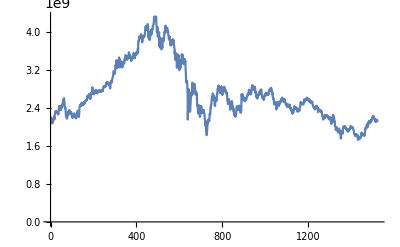

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered1HourCandle]
```

```mathematica
rsWethUsdc90dFiltered1HourCandle = Differences[Log[twapsWethUsdc90dFiltered1HourCandle]]
```

{-0.0012941,-0.00939344,-0.0241963,-0.0104817,-0.0147229,0.00820584,0.014547,0.00112845,-0.0193036,0.0015467,0.0227744,0.00588498,0.0156569,-0.00128477,0.00383628,0.00765843,-0.0210875,0.0282886,0.0179942,0.00895628,0.0123902,0.00146154,0.00885738,-0.00492522,0.00591001,-0.0150075,0.00572474,-0.00151273,-0.00691957,0.000305489,0.00603401,-0.0100807,0.000682628,0.00289066,-0.0146574,0.0102704,0.0344637,0.00778817,0.0186024,0.00506249,-0.00892867,-0.00431243,0.00701086,-0.0161606,-0.00113936,-0.012692,0.000360494,0.0312663,-0.0188007,0.00704985,0.010712,0.0109927,0.00574422,-0.00522957,-0.00581162,0.0174255,0.0193901,0.0145689,-0.00244056,0.00546382,0.00668475,0.00364873,-0.0249162,-0.011591,-0.0228768,-0.0253583,0.00692255,0.00215623,-0.0106241,-0.0478116,-0.0183125,0.00791559,-0.0236331,-0.00521017,-0.00563152,-0.00177441,0.0111625,0.0321856,0.00678772,-0.0188758,0.00455526,0.0139082,0.0189708,-0.0114339,0.0166378,0.00651145,-0.00655183,-0.0117856,0.00907496,-0.0115368,-0.0149498,-0.00193373,0.0155644,0.0014861,0.00242527,-0.0157198,0.00129305,-0.00477816,-0.017937,-0.0152772,0.00743036,0.00291753,-0.00947762,0.0187403,-0.00177333,0.0103974,0.00629432,-0.0000214817,0.00563643,-0.0111222,-0.0124043,-0.00699624,0.00972473,-0.00190175,-0.0202832,0.00107855,0.00241894,-0.00819129,0.00840919,0.00967682,0.022379,0.00234826,0.0144718,0.0013018,0.0111105,0.000332482,-0.000134127,-0.0102255,-0.00747374,-0.0100704,-0.0290967,0.0216257,0.0169805,0.0462855,0.0155823,0.00060125,0.00484828,-0.00178179,0.00678203,-0.00217996,-0.00778384,-0.00111525,0.0178142,0.0111511,-0.00443252,-0.00200192,-0.00437384,0.000538142,0.00743398,-0.0025352,-0.00431194,-0.0106806,0.0113255,0.00980401,0.00225378,-0.0040591,0.00357938,-0.00524702,-0.00368089,0.0102967,0.0115506,-0.000148314,-0.00216172,0.00130508,-0.000413909,0.00828751,-0.0031985,0.00176965,0.0259262,0.00826952,-0.00689629,-0.000758883,-0.0049228,0.00453319,0.000734732,-0.00383704,0.0191525,0.00630641,-0.00544079,-0.0157458,-0.0000538651,-0.013288,-0.00261155,0.00789323,-0.00689467,0.00818365,0.0234902,0.0130463,-0.00754792,0.00245135,-0.00598091,0.0106099,0.00386107,0.0396993,-0.0452123,0.00766826,-0.00403656,0.00603463,-0.00466538,-0.00261885,-0.00127849,-0.0101564,0.00372127,0.00926992,0.00267257,-0.00477485,0.0167269,0.000933011,0.000192249,0.00685637,-0.00820991,0.00507312,-0.00432025,-0.0110354,-0.00698569,0.00250417,-0.00504121,0.00877336,0.0102957,-0.00281021,-0.00562736,0.0014454,-0.000400875,0.00569195,0.0028523,0.00599179,-0.00135385,0.001688,-0.00510824,-0.00174067,-0.00699027,0.000740825,0.00267789,-0.002698,0.00236155,0.00446606,0.000211853,0.00457926,-0.00472001,-0.00303777,-0.00106019,0.00611192,-0.00101119,0.0221515,0.00269457,0.00191348,0.00686818,-0.00212883,-0.0000333065,-0.00590221,-0.000872327,0.00443358,0.00618739,0.000978685,-0.00137111,-0.0044582,0.0121537,0.012713,0.00281359,-0.00333111,0.00492416,-0.00217514,0.00410975,-0.00148692,-0.000771305,0.00484947,-0.013151,0.00154328,0.000245555,-0.00789836,-0.00759518,0.00433302,0.0104016,0.00181102,0.00161976,-0.00315996,-0.0351516,0.040803,0.000546262,0.00344737,0.0094448,-0.00133529,0.00172134,-0.010834,0.00855037,0.00834883,0.00846601,0.00723202,0.00469582,0.00866432,0.00337486,0.0137537,0.0143363,-0.00356706,-0.00568652,0.00479291,-0.00924879,-0.00506178,0.0161896,0.00296944,0.0274497,0.0125781,-0.00409099,-0.00385356,0.00556396,0.0256687,0.00661141,-0.0292281,-0.0097714,-0.0121292,0.0112151,0.0245253,0.00573675,-0.00730707,-0.0144401,0.0148419,0.0156641,0.0142715,0.0035959,-0.00952215,-0.0355128,-0.018082,0.0161683,0.0166066,0.0108901,-0.00637733,-0.0220459,-0.00396726,0.00237482,0.017944,-0.0103872,-0.00866101,-0.00940875,-0.0026819,0.00568391,0.0228077,0.00280706,0.00265709,-0.00284089,0.00308071,-0.00696032,-0.00304267,0.00569525,0.0192498,-0.00288628,0.0126126,-0.00040282,-0.00271909,0.0212392,-0.00410335,-0.0098011,0.00538715,-0.00559571,0.00228718,-0.00763678,-0.00945856,0.00588384,0.00175553,0.00902914,0.0057251,0.000756119,-0.00426355,0.00958883,0.0160935,0.000343066,-0.0196071,-0.0136214,0.00194127,0.0133585,0.00178386,-0.00367229,-0.00526729,-0.0103905,-0.00592555,-0.0111679,0.00562247,0.00843029,0.00384391,-0.00631954,0.00711197,0.0000715682,-0.0018841,0.0124739,0.00168979,0.00267713,0.0150261,-0.00165389,-0.00858756,-0.00185717,-0.00396376,-0.00542598,-0.0101666,0.00963832,0.0123639,0.0037379,-0.00233891,0.0105406,-0.00628502,-0.00515027,0.000879561,0.00949945,-0.00138879,-0.00474051,0.000717644,0.0100192,0.020237,-0.0207963,0.052254,0.0130797,0.00232995,-0.0022154,0.0110306,0.0111614,-0.00767684,-0.00335574,0.00415127,0.00346162,-0.000483502,0.00326224,0.00668189,0.00668463,-0.00201467,-0.00880873,-0.00675781,0.00155063,-0.028712,0.00572009,0.00688331,0.0153514,0.00813714,-0.00248631,-0.006763,-0.000375609,0.00737534,-0.00385056,0.0019901,0.000198811,0.00510032,0.0116912,0.0188459,0.0134263,0.00366521,-0.0000202228,-0.00434395,0.00492858,-0.0108023,-0.00670333,0.018204,-0.000340032,-0.0104199,0.0218255,-0.0010619,-0.00754958,-0.012836,-0.0487143,0.028263,-0.00545802,-0.00530323,-0.018157,-0.00673611,-0.00679897,0.017294,-0.00188778,0.013879,-0.00355901,0.00637078,0.022872,-0.0133469,-0.0113365,0.00262367,0.00972989,0.0100581,-0.0018835,0.00807372,-0.000664149,0.0169381,-0.00386746,0.00511166,0.00789178,0.0026353,0.0192524,0.0135869,-0.0000334813,0.00175676,-0.00480754,-0.00364428,-0.00087381,-0.00858292,0.00584471,0.00225291,0.0103889,-0.0291231,-0.0156554,-0.00598179,-0.0289033,0.0182389,0.00843401,-0.00189759,-0.0486656,0.00656987,0.0150269,-0.00573566,-0.00699279,0.00348541,0.0114188,-0.0766094,0.0495032,-0.034843,-0.0224625,0.024264,0.0140562,0.0153153,-0.0227438,-0.0117354,-0.0212833,-0.00807792,0.0121961,0.016902,-0.0029743,-0.0187685,0.0345767,0.0192089,-0.0143146,-0.00200294,-0.00243474,0.0114072,0.000437347,0.0119957,0.0175754,0.00207719,0.0121896,-0.00628157,0.0115755,0.0183623,0.0071341,-0.00367281,-0.00846574,-0.00714214,-0.0132724,0.00961144,0.0102557,-0.00102612,0.00126949,0.0000786298,-0.0108557,-0.00365595,-0.00285802,-0.0177863,-0.00735803,-0.00228951,-0.0161318,0.0086849,0.00837138,-0.00626809,0.00255444,-0.0226809,-0.0157427,0.000574938,-0.0089521,0.0216996,0.00161998,-0.0215092,0.00525226,0.0196051,0.00162947,-0.00505536,0.00102626,0.00228188,0.00799437,-0.00959126,-0.000373717,0.00650619,-0.00530254,-0.0203736,-0.00673919,-0.0106307,-0.00825197,-0.0283604,0.0138139,-0.0336105,-0.0165539,-0.00108657,0.0363906,0.00522162,-0.012247,-0.0279668,-0.011188,-0.0392792,0.0140206,0.0248475,0.0245239,0.0192418,-0.00573792,-0.0103429,0.0123291,-0.0138041,-0.0169138,-0.0184294,-0.024684,-0.0204641,0.0455715,0.00947227,0.0104339,-0.0379973,-0.0128265,0.0264401,0.0143223,-0.000668989,0.00541914,0.0272934,0.0125127,-0.0132218,0.00480567,-0.0121086,0.00699344,0.00849575,-0.0214613,-0.0243592,-0.0104821,0.0124331,0.0154605,-0.0161291,0.00399398,0.0153613,-0.00573467,-0.0114158,0.00803497,-0.0299383,-0.0348267,-0.0234018,-0.0415037,-0.0173636,0.011688,-0.00286386,0.00392249,-0.00813305,-0.0471791,-0.0499205,-0.214646,0.0919721,0.104027,0.0650292,-0.0185358,-0.0492683,0.00774173,-0.0460781,0.0524762,-0.0379616,-0.0963281,0.00422759,0.0494469,0.0260708,0.0376831,0.0104027,0.0338998,-0.021013,-0.00332139,0.01251,0.040997,0.0436868,-0.0053785,-0.0279027,-0.0510988,0.0240177,0.0118012,-0.00254107,0.00992314,-0.0105293,0.00703635,0.035696,-0.0147688,-0.0226959,-0.01217,-0.00813089,-0.00256247,-0.0211896,0.0202049,0.00410991,-0.0235389,-0.00232114,0.00806105,-0.0708791,-0.0258258,0.0048203,-0.00910545,-0.0214291,-0.0437344,0.0135306,0.0344801,0.00460629,0.0128563,0.0057863,-0.0365698,-0.0351768,-0.0316194,0.00220857,0.0172454,0.0350072,0.00549788,0.0367225,-0.00607989,0.00453372,-0.0209481,-0.0183107,0.00915097,-0.0292831,-0.000930007,0.00429248,0.0232195,-0.00296,-0.00318207,-0.0158749,0.0247332,-0.021289,0.000367848,-0.0147724,-0.020053,-0.0147157,-0.0291446,-0.0479736,0.0163756,0.0263655,-0.0368352,-0.06705,0.0206743,-0.0197836,-0.0485451,0.0407481,0.00476796,0.0439972,0.0477376,0.00724105,-0.0115687,0.0326188,-0.0176598,0.00578556,0.0148619,-0.0177211,-0.0011764,0.0370896,0.036244,-0.00502727,-0.00928528,0.0330669,0.03636,-0.000794619,0.0200143,0.000775624,0.0140905,0.0272715,0.0137846,0.00845554,-0.00979266,-0.00047401,0.0413373,-0.0110942,-0.0290495,-0.0077595,-0.000493834,0.0186925,0.011148,-0.00858051,-0.0238053,-0.0400413,-0.0107169,-0.0010372,0.0434581,0.0216406,-0.00891953,-0.00538814,0.00949722,-0.0167082,-0.000775799,0.0277059,0.0305213,-0.00536035,0.00837233,0.0325365,0.00744402,-0.00663069,0.00509895,0.0206239,-0.00414016,-0.00369765,-0.0173349,0.0110792,-0.0129434,-0.0182479,-0.00515184,-0.0029229,-0.0047764,0.00572359,0.00681618,0.0175886,0.00939277,0.0120975,-0.0174053,-0.0306361,-0.0131389,-0.00500391,0.00414471,0.0148534,0.0060136,0.00300095,0.013594,0.00160629,0.00906468,-0.00317154,0.0137047,-0.00813121,-0.0142553,-0.00152433,0.00109081,-0.0113489,-0.00768726,0.0154724,-0.00688117,-0.0120338,-0.00927645,0.00904654,-0.00194751,-0.0151355,-0.0211195,-0.0256399,0.00274905,-0.0289856,0.00311602,-0.00484641,0.0188107,0.0240086,-0.01353,-0.00600392,-0.0178883,0.00041605,0.00735817,-0.0161636,-0.0455257,0.00873186,0.0188407,0.0321121,0.00133565,0.00256067,-0.00364937,0.0142829,-0.0036941,-0.0170464,-0.0201625,-0.00710644,-0.00288611,0.00284228,-0.0230984,0.00433128,-0.0275039,0.0115466,-0.0319235,-0.00771588,-0.00844404,0.00730837,0.00638166,0.00925695,-0.0312138,0.0026566,0.0245846,0.0044872,0.0166774,0.0285583,0.0156512,0.00328341,-0.00500426,-0.00644106,0.00348683,-0.00596326,-0.00774951,-0.0123055,0.00964994,0.0141724,0.0106783,0.00466503,-0.00418728,-0.00407016,-0.0118364,-0.00637561,-0.0176246,-0.0184907,0.000268613,-0.00127051,0.00865545,0.0164549,0.089497,0.0423522,-0.0208488,2.12254×10^-6,0.0053921,0.0132907,-0.0124978,-0.0225969,-0.00816368,0.0101791,0.00440036,-0.018623,0.0234938,-0.020197,-0.00305135,-0.00710412,0.00858124,-0.00790235,0.00936683,0.00833752,0.00302318,0.0046938,-0.0171702,0.0142753,0.00676129,0.00208907,0.00116304,0.0052074,0.016854,0.00298927,-0.00299108,-0.00278577,0.00832414,0.00609375,0.0115385,0.011892,-0.00795538,0.0000639027,-0.000167785,-0.0050155,-0.00898109,-0.00827721,0.00284233,-0.0033578,-0.00527723,0.00754765,0.017464,0.0179267,0.0106031,-0.00252356,0.00677932,0.0133633,-0.0185224,-0.00346057,-0.010544,-0.000770574,0.00092748,0.013321,-0.00180188,-0.0111563,0.00177417,0.0101783,0.00248479,0.00551513,-0.0217116,-0.0238835,0.0087551,-0.000164684,-0.0264604,-0.0163268,-0.0023619,0.00124636,0.00794775,-0.00562918,-0.0134513,0.0201362,-0.00701217,0.0087424,0.00377169,0.0111149,0.00102107,-0.00436573,0.0119223,0.00170911,-0.0141093,0.0196286,0.00901403,-0.00188142,0.0023976,0.00356037,-0.00246373,0.0055925,0.00277649,-0.000521804,-0.029022,-0.0196281,-0.0074488,-0.00516444,-0.00697616,0.0127463,-0.00540212,0.000105092,-0.000996741,0.000947258,-0.0220139,0.00555942,0.0141572,0.0108638,0.012686,-0.00311328,0.00234005,0.000526961,-0.00682497,0.0103438,0.0120844,-0.0013824,-0.00490355,-0.0021672,-0.0114053,0.00858744,0.0103122,-0.00173041,-0.0097833,-0.00242831,-0.000637409,0.00877699,-0.00661491,0.00785111,0.0165937,0.0112232,0.00119587,-0.00423626,-0.000676788,0.000379677,-0.00691273,0.000358558,0.0124191,0.0117715,-0.00437439,0.00298034,-0.0154748,-0.000468342,-0.00389883,-0.0153326,-0.00978585,0.00777336,-0.0266987,-0.0118,-0.00126481,-0.00889627,0.00484177,-0.0158411,-0.0327195,0.0104915,-0.00744525,-0.000632951,0.0159287,-0.00309067,-0.00571841,0.00117362,0.00538867,-0.0173576,-0.0379915,-0.00591382,0.0147172,0.00804599,0.01915,0.0113871,0.0111423,-0.0115324,0.00952897,-0.0201143,-0.00961352,-0.00036019,-0.00174056,0.00804524,0.0139242,0.011378,-0.0131077,-0.0000160461,0.00421173,0.0171157,-0.00359611,-0.00450502,0.0100182,0.0161194,-0.00038198,-0.0080995,-0.00325895,0.0032708,0.0187834,-0.0177846,0.0047134,-0.00175758,-0.00215127,-0.002971,-0.0101417,-0.00356038,0.00407345,-0.0046887,0.00180119,0.0208902,-0.0095054,-0.00642249,-0.00569552,-0.00644413,-0.0109336,-0.00971393,-0.000142314,-0.00206448,-0.00499903,0.0111543,0.00523848,-0.00724996,-0.0212392,-0.000328258,0.0165968,0.00478763,-0.000135959,-0.0144011,0.00521025,0.00303424,0.00504557,0.00101508,-0.00530451,0.00465818,-0.00600279,-0.0149278,-0.0145622,0.00621787,0.0043072,-0.00398839,-0.0197602,0.00455476,-0.00817934,-0.00175919,-0.0218371,-0.00129088,0.00380165,-0.00276214,0.00160008,0.0102873,-0.000637267,0.00245463,0.0277299,0.00871102,0.0130382,-0.00762243,-0.00411295,-0.00806793,0.000724258,0.00890668,0.0024938,-0.0017114,-0.00420394,-0.00767731,-0.00283168,0.000116806,0.0109929,-0.00999281,-0.0198979,-0.0018207,-0.004514,0.00696894,0.00263064,0.00469954,0.0061506,-0.00027183,-0.00254488,-0.0023037,-0.00673069,0.00832445,0.0166375,0.012955,0.00133117,0.0204564,0.0184066,-0.00762892,-0.00361871,-0.000792056,0.000915494,-0.0050559,-0.00387898,0.00533813,0.00161225,0.000383698,-0.00680211,-0.00227587,0.00517242,-0.00301902,0.0137127,0.0192007,-0.00261384,0.0098416,-0.00418281,-0.00649396,-0.00881918,0.00525002,0.0062008,0.000847117,0.0105118,0.00212531,-0.00584622,0.00375379,0.00790757,0.00296729,-0.0000764963,-0.00271195,-0.0109511,0.000704812,-0.00167003,0.00222784,0.00217801,-0.0129713,-0.00677012,0.00435604,0.0105383,-0.000958673,-0.0198356,-0.000219197,0.00543539,0.00542252,-0.0110759,-0.00457577,0.00394839,-0.00247434,0.00338092,0.000203,0.00309958,0.0012171,-0.0051046,-0.00532081,-0.018683,-0.00681364,0.00306327,-0.0101975,-0.00179384,-0.0103758,0.00326322,0.00528367,-0.00801237,0.000974888,-0.0150801,0.00572861,0.00801428,0.00720188,0.00488335,-0.0038248,0.00304976,0.008319,-0.003844,-0.000822836,-0.000341455,-0.0122885,-0.010619,0.00328207,0.00571093,-0.0383092,0.00206379,0.00986234,-0.00021928,-0.000416232,0.000495876,0.0116051,-0.00114484,-0.0125009,-0.00100441,0.00348239,0.00568923,-0.00638835,-0.00304277,0.00627256,-0.00804012,-0.00847842,0.00527838,-0.0145063,-0.00815206,-0.00955673,-0.0113306,0.00273622,-0.0147734,-0.0178795,0.0121509,0.00866658,0.002415,0.00570551,0.0102709,0.00162146,-0.0140716,-0.0130787,0.00989884,0.0130122,-0.00343047,0.00571281,-0.000135609,-0.00639472,0.00344081,0.00400718,-0.0060211,0.00745442,-0.00343697,-0.00171008,-0.013836,0.00134676,0.00332667,0.00249885,-0.0159085,-0.00496909,-0.00733892,0.00896781,-0.00346551,0.00697238,0.00969443,0.000614359,-0.00351155,-0.00262461,-0.00790318,-0.0290954,-0.0159504,-0.00936422,0.010574,0.00720206,0.00781923,0.00411121,0.00422791,0.0193097,0.0295205,0.0069152,-0.00207255,-0.00397921,-0.00675426,-0.00784839,-0.0117904,-0.0186685,-0.0206979,0.00559483,-0.0452594,-0.0010944,-0.00594529,-0.014065,-0.0193764,0.00814122,0.0119351,0.0106061,-0.014344,-0.0194366,0.000392771,0.00115321,0.00254537,-0.0213141,-0.00774783,0.0010795,0.0242412,0.00756068,0.00972191,-0.000957534,-0.00956901,-0.0022591,-0.00241011,-0.0296387,-0.00680816,0.0109481,-0.0264686,-0.0365919,-0.00945587,0.0609892,0.0177554,0.00230833,0.00833756,-0.00480724,-0.0055726,-0.0105714,-0.00944353,0.03484,0.0336373,0.00603512,0.00072387,0.00130216,0.00372819,-0.00523813,-0.0106538,0.00301437,0.00365843,0.000404859,0.00548513,-0.0101902,-0.00418997,0.000906365,-0.0120625,-0.00622167,-0.00935106,0.00463923,0.00322816,0.00808523,-0.00803339,-0.0186717,-0.0064605,0.00310783,0.00286737,0.00662379,0.00419559,0.000083875,0.00737759,-0.00348675,0.0125808,0.00331526,-0.00209701,0.0123044,0.000232928,0.0157637,-0.000590066,-0.00301766,-0.00455768,-0.0041327,-0.0072383,0.00646061,-0.00753522,0.00951817,-0.00137874,-0.00511877,-0.00798561,-0.00397857,-0.0127422,-0.00381603,-0.00905081,-0.0200314,-0.00725568,-0.00620233,0.00283735,-0.0194601,-0.00252828,0.00134175,0.0128666,0.00482291,0.00206355,-0.00714427,-0.0139373,0.00450107,-0.0051638,0.00372823,0.00907861,-0.00421693,-0.0358477,-0.0202306,0.0154573,0.00629004,0.0162906,-0.00386356,-0.0252872,0.015652,-0.0121158,0.00631525,0.0135046,-0.00181622,-0.0113363,0.00306231,0.0101013,0.0202928,0.0106909,0.0177692,0.00459609,-0.00705124,-0.00600908,0.00332132,-0.0146672,-0.00887911,0.00689624,0.0099005,-0.00781295,-0.00185977,0.00283063,-0.00792733,-0.00574474,-0.000458045,0.00459319,0.00116538,0.0610492,0.0132503,0.00885643,-0.00814342,0.00331463,-0.000853562,0.000575169,0.022219,-0.000594212,0.0203352,-0.00409039,-0.0250254,-0.000313955,0.00619466,0.0028855,0.0266109,0.0185151,-0.00735743,-0.00385612,0.0166255,0.00333954,-0.0103708,-0.0127511,0.0120388,0.00851822,-0.00747829,-0.0010489,0.00688954,-0.00481085,0.0221793,-0.0123116,0.00736885,0.00545394,0.010248,-0.00149937,0.0146894,0.00636515,-0.00309933,0.0041733,0.000818091,-0.00416369,0.000715836,-0.00952928,-0.00844322,-0.0065269,0.00283923,-0.00539034,-0.00282712,-0.0124691,-0.0104712,0.0138421,0.00717897,-0.0038457,-0.00942509,0.00704325,0.00803376,-0.0100288,0.000751933,-0.014457}

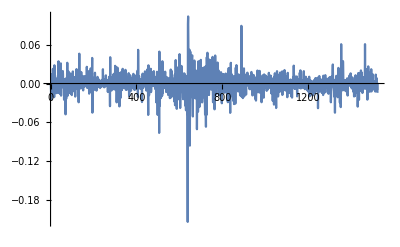

```mathematica
ListLinePlot[rsWethUsdc90dFiltered1HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered1HourCandle = EstimatedDistribution[rsWethUsdc90dFiltered1HourCandle, StableDistribution[1, aWU90dC1h, bWU90dC1h, locWU90dC1h, scaleWU90dC1h]]
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
(* Interesting ... compound less on the funding payments, have more leeway. How does that make sense wrt inverse cdf exponentiation? *)
```

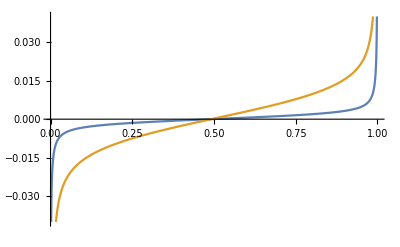

```mathematica
Plot[{InverseCDF[edistWethUsdc90dFiltered,x],InverseCDF[edistWethUsdc90dFiltered1HourCandle,x], InverseCDF[edistWethUsdc90dFiltered4HourCandle,x]},{x,0,1.0}, PlotRange->{-0.04, 0.04}]
```

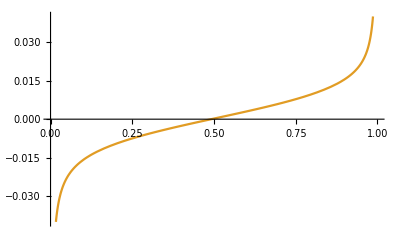

```mathematica
Plot[{, InverseCDF[edistWethUsdc90dFiltered1HourCandle,x]},{x,0,1.0},  PlotRange->{-0.04, 0.04}]
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandle,0.99]
```

0.0472398

```mathematica
InverseCDF[edistWethUsdc90dFiltered,0.99]
```

0.0124991

```mathematica
Exp[0.012499142980299232]
```

1.01258

```mathematica
Exp[0.1072270317901139]
```

1.11319

```mathematica
(* Hmmm, so maybe plot e^(mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)) as a function of update times T. What does this tell us vs d we're looking for? *)
```

```mathematica
edistWethUsdc90dFiltered1HourCandle
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
(* Define mu, sig functions for exponential term in d *)
```

```mathematica
mu[a_, loc_] := loc
```

```mathematica
sig[a_, scale_] :=scale/( 1/a)^(1/a)
```

```mathematica
(* Apply to our case *)
```

```mathematica
muWethUsdc90dFiltered1HourCandle = mu[1.597679462042982, -0.00015725436055898914]
```

-0.000157254

```mathematica
sigWethUsdc90dFiltered1HourCandle = sig[1.597679462042982,0.007900125269736371]
```

0.0105925

```mathematica
aWethUsdc90dFiltered1HourCandle = 1.597679462042982
```

1.59768

```mathematica
edistWethUsdc90dFiltered1HourCandleNormalized = StableDistribution[1,aWethUsdc90dFiltered1HourCandle,0,0,1]
```

StableDistribution[1,1.59768,0,0,1]

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandleNormalized,0.90]
```

1.98681

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandleNormalized,0.95]
```

2.81905

```mathematica
InverseCDF[edistWethUsdc90dFiltered1HourCandleNormalized,0.99]
```

6.31376

```mathematica
factorWethUsdc90dFiltered1HourCandle[t_, alpha_]:= Exp[muWethUsdc90dFiltered1HourCandle*t + sigWethUsdc90dFiltered1HourCandle * (t/aWethUsdc90dFiltered1HourCandle)^(1/aWethUsdc90dFiltered1HourCandle) * InverseCDF[edistWethUsdc90dFiltered1HourCandleNormalized,1-alpha]]
```

```mathematica
factorWethUsdc90dFiltered1HourCandle[1, 0.01]
```

1.05098

```mathematica
(* TODO: Redo this analysis! ... Below is in line with 4 hour candle above :) *)
```

```mathematica
factorWethUsdc90dFiltered1HourCandle[4, 0.01]
```

1.12542

```mathematica
factorWethUsdc90dFiltered1HourCandle[8, 0.01]
```

1.19967

```mathematica
(* Over 24 hours you can see the difference substantially at different confidence levels ... *)
```

```mathematica
factorWethUsdc90dFiltered1HourCandle[24, 0.01]
```

1.4345

```mathematica
factorWethUsdc90dFiltered1HourCandle[24, 0.10]
```

1.11735

```mathematica
factorWethUsdc90dFiltered1HourCandle[24, 0.05]
```

1.17235

```mathematica
(* VaR at 95% seems good here in terms of usability for trading. 15% draw down in a day worst case on ETH/USDC is not terrible in terms of funding rate max *)
```

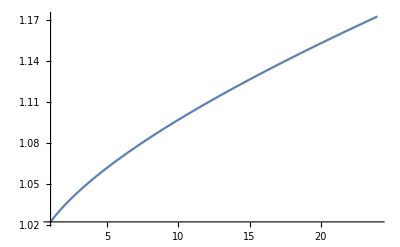

```mathematica
Plot[factorWethUsdc90dFiltered1HourCandle[t, 0.05], {t, 1, 24}]
```

```mathematica
(* Interesting S shape here ... Due to the Exp[t^(1/1.5)] term *)
```

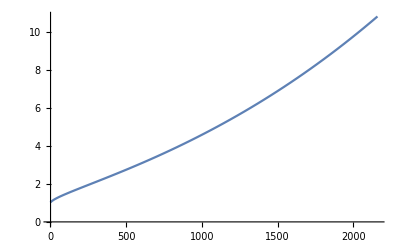

```mathematica
Plot[factorWethUsdc90dFiltered1HourCandle[t, 0.05], {t, 1, 24*30*3}]
```

```mathematica
(* So takes on order of 2 months to reach a 5x price cap on price bracket amount *)
```

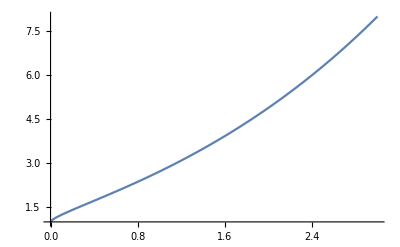

```mathematica
Plot[Exp[(t)^(1/1.5)], {t, 0, 3}]
```

```mathematica
(* This is where caps become very good :) *)
```

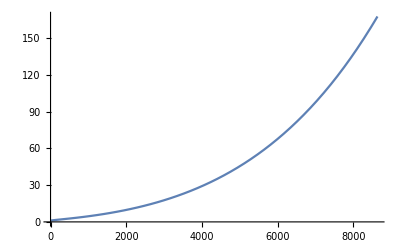

```mathematica
Plot[factorWethUsdc90dFiltered1HourCandle[t, 0.05], {t, 1, 24*30*12}]
```

```mathematica
(* Plot k AND (1-k)^m where m is diff depending on number of times we compound *)
```

```mathematica
(* Assume k min is determined by factor value at 95% confidence for different number of periods T *)
```

```mathematica
dmin95WethUsdc90dFiltered1HourCandle[t_] := factorWethUsdc90dFiltered1HourCandle[t, 0.05]
```

```mathematica
kmin95WethUsdc90dFiltered1HourCandle[t_] := (1-1/dmin95WethUsdc90dFiltered1HourCandle[t])/2
```

```mathematica
(* Look at different time periods ... 1 (1h), 4 (4h), 6 (6h), 8 (8h), 12 (12h), 24 (1d), 168 (7d) *)
```

```mathematica
kmin95T1hWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[1]
```

0.0109354

```mathematica
kmin95T4hWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[4]
```

0.0255287

```mathematica
kmin95T6hWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[6]
```

0.0325961

```mathematica
kmin95T8hWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[8]
```

0.0387123

```mathematica
kmin95T12hWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[12]
```

0.0492077

```mathematica
kmin95T1dWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[24]
```

0.0735077

```mathematica
kmin95T7dWethUsdc90dFiltered1HourCandle = kmin95WethUsdc90dFiltered1HourCandle[168]
```

0.203882

```mathematica
(* Interesting ... around minimum of 3.26% every 6 hr compounding. Can work with that to have some buffer in event bad fit *)
```

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandle[t_, m_] := 1-(1-kmin95WethUsdc90dFiltered1HourCandle[m])^(Floor[t/m])
```

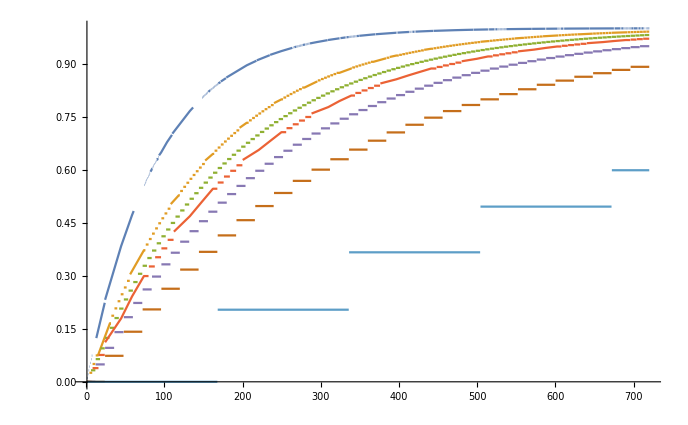

```mathematica
Plot[{drawDownMin95WethUsdc90dFiltered1HourCandle[t, 1],  drawDownMin95WethUsdc90dFiltered1HourCandle[t, 4],  drawDownMin95WethUsdc90dFiltered1HourCandle[t, 6], drawDownMin95WethUsdc90dFiltered1HourCandle[t, 8], drawDownMin95WethUsdc90dFiltered1HourCandle[t, 12], drawDownMin95WethUsdc90dFiltered1HourCandle[t, 24], drawDownMin95WethUsdc90dFiltered1HourCandle[t, 168]}, {t, 1, 24*30}]
```

```mathematica
(* Should like compare ratio of price bracket to d^(t/m). When set m for d, setting point at which d^m = price bracket[m].. But d is NOT an interest rate... k = (1-1/d)/2 makes this interesting in terms of traders view on draw down to their OI ... *)
```

```mathematica
(* Plot the actual interest rates seen per day for different values of m *)
```

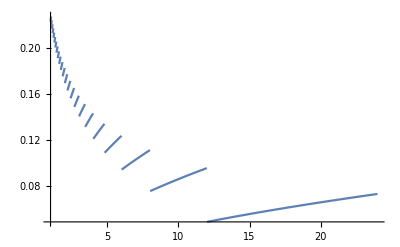

```mathematica
Plot[drawDownMin95WethUsdc90dFiltered1HourCandle[24, m], {m, 1, 24}]
```

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandle[24, 1]
```

0.231947

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandle[24, 4]
```

0.143723

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandle[24, 8]
```

0.111699

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandle[24, 12]
```

0.095994

```mathematica
(* Floor is making this visual difficult. Make continuous for plot purposes ... *)
```

```mathematica
drawDownMin95WethUsdc90dFiltered1HourCandleContinuous[t_, m_] := 1-(1-kmin95WethUsdc90dFiltered1HourCandle[m])^(t/m)
```

```mathematica
(* Below is min funding rate required extended to per day rate, if apply funding payment every m hours  *)
```

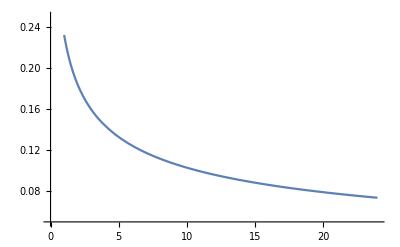

```mathematica
Plot[drawDownMin95WethUsdc90dFiltered1HourCandleContinuous[24, m], {m, 1, 24}, PlotRange->{0.05, 0.25}]
```

```mathematica
(* Less we compound, smaller max DAILY funding rate needed to overcome price bracket changes. But more short term (<1d) we likely take *)
```

```mathematica
(* Generalize this for any confidence level (not just 95%) *)
```

```mathematica
dminWethUsdc90dFiltered1HourCandle[t_, alpha_] := factorWethUsdc90dFiltered1HourCandle[t, alpha]
```

```mathematica
kminWethUsdc90dFiltered1HourCandle[t_, alpha_] := (1-1/dminWethUsdc90dFiltered1HourCandle[t, alpha])/2
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[t_, alpha_, m_] := 1-(1-kminWethUsdc90dFiltered1HourCandle[m, alpha])^(Floor[t/m])
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandleContinuous[t_, alpha_, m_] := 1-(1-kminWethUsdc90dFiltered1HourCandle[m, alpha])^(t/m)
```

```mathematica
(* If fit to 8h compounded rate but still pay every 10min, how much is k? (k paid every 10 min but use 8h compounding amount) *)
```

```mathematica
(* Function to rescale k min calibrated using factor's value at time m in the future. But then applied over shorter time span < m *)
```

```mathematica
(* d_shorter^(#periods of short in long) = d_longer; m > t here *)
```

```mathematica
rescaledKminWethUsdc90dFiltered1HourCandle[t_, alpha_, m_] := (1-1/(dminWethUsdc90dFiltered1HourCandle[m, alpha])^(t/m))/2
```

```mathematica
rescaledKminWethUsdc90dFiltered1HourCandle[1/6, 0.05, 8]
```

0.000838735

```mathematica
(* Calculate effective funding rate after 8 hours applied every 10 min *)
```

```mathematica
1-(1-rescaledKminWethUsdc90dFiltered1HourCandle[1/6, 0.05, 8])^(6*8)
```

0.0394759

```mathematica
(* Compare with draw down applied only once every 8 hours *)
drawDownMinWethUsdc90dFiltered1HourCandle[8, 0.05, 8]
```

0.0387123

```mathematica
(* Looks good *)
```

```mathematica
(* Plot price bracket * d^(t/m) over time t *)
```

```mathematica
(* Look at funding rates needed over different confidence levels, to compare *)
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.01, 8]
```

0.229456

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 8]
```

0.111699

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.10, 8]
```

0.0800559

```mathematica
(* Last 95 -> 99% is what ramps it up significantly *)
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.01, 1]
```

0.445257

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 1]
```

0.231947

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.10, 1]
```

0.169511

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 24]
```

0.0735077

```mathematica
(* Similar with rescale. See if applied every 10 min for 8 hour value but after 1 d, 7d, 14d what drawdown is *)
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 8]
```

0.111699

```mathematica
1-(1-rescaledKminWethUsdc90dFiltered1HourCandle[1/6, 0.05, 8])^(6*24)
```

0.113814

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24*7, 0.05, 8]
```

0.563564

```mathematica
1-(1-rescaledKminWethUsdc90dFiltered1HourCandle[1/6, 0.05, 8])^(6*24*7)
```

0.570786

```mathematica
(* Beautiful. Anchoring at factor value at m sets funding rate to be min. Does compound surpass price bracket at the 8 hour mark? *)
```

```mathematica
(* Look at rescaled draw down first to make sure consistent *)
```

```mathematica
rescaledDrawDownMinWethUsdc90dFiltered1HourCandle[t_,alpha_, m_, anchor_ ]:= 1- (1-rescaledKminWethUsdc90dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
rescaledDrawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.113589

```mathematica
rescaledDrawDownMinWethUsdc90dFiltered1HourCandle[24*7, 0.05, 1, 8]
```

0.570023

```mathematica
(* Great. 1h funding payments on 8h anchor look great *)
```

```mathematica
(* Look at (1 - 2k)^m over time .... Compound factor for different compound intervals. Assume funding payments applied every 1 h for simplicity with fits. *)
```

```mathematica
compoundFactorMinWethUsdc90dFiltered1HourCandle[t_, alpha_, m_, anchor_]:= (1-2*rescaledKminWethUsdc90dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
(* 8h payment at 95% confidence of VaR led to drawdown of 11% worst case due to funding. Use alpha=0.05, m=8. Rescaled funding st paid every 1 h *)
```

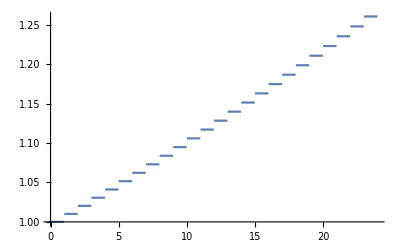

```mathematica
Plot[{1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

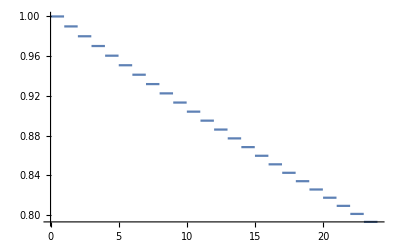

```mathematica
Plot[{compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

```mathematica
drawDownMinWethUsdc90dFiltered1HourCandle[24, 0.05, 8]
```

0.111699

```mathematica
1-compoundFactorMinWethUsdc90dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.214754

```mathematica
(* Perfect. Draw down to OI imbalance should be about 2 times draw down to OI on a side *)
```

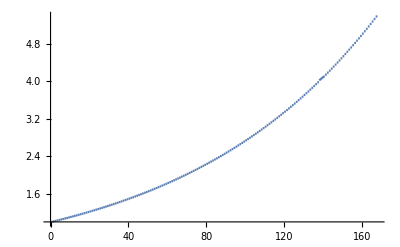

```mathematica
Plot[1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*7}]
```

```mathematica
(* Plot price bracket ...  *)
```

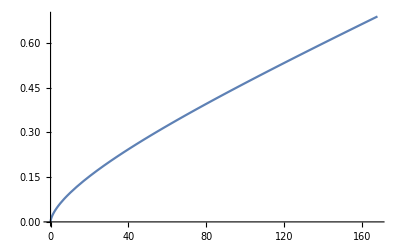

```mathematica
Plot[factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1, {t, 0, 24*7}]
```

```mathematica
(* Plot 1/compoundFactor vs price bracket *)
```

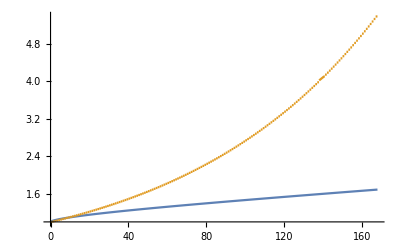

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

```mathematica
(* Look at the earlier times ... *)
```

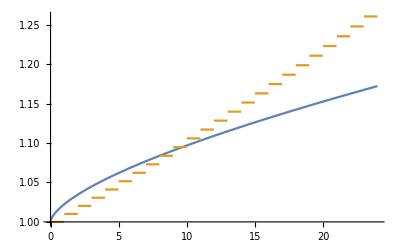

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

```mathematica
(* Look at later times ... *)
```

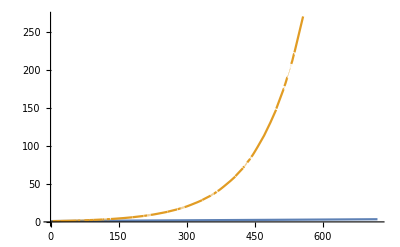

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* and the product of the two to make sure decreasing over time ... *)
```

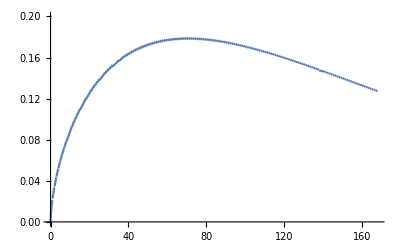

```mathematica
Plot[(factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*7}, PlotRange-> {0, 0.2}]
```

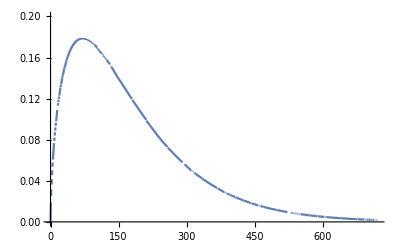

```mathematica
Plot[(factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*30}, PlotRange-> {0, 0.2}]
```

```mathematica
(* Compare with draw down over time *)
```

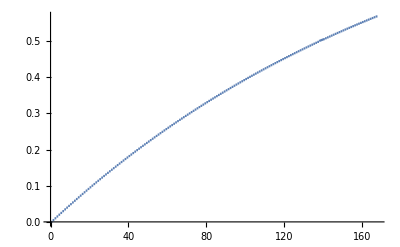

```mathematica
Plot[{rescaledDrawDownMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

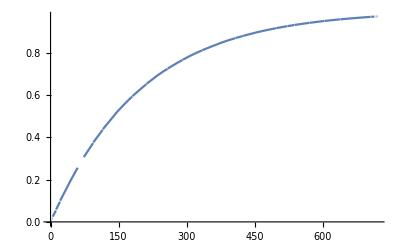

```mathematica
Plot[{rescaledDrawDownMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* Anchor used in k is everything. What is the interpretation? Time when d^m is exactly equal to first term in price bracket[m]. Then d^m surpasses greatly in size as m -> infty *)
```

```mathematica
(* So look at 1/compoundFactor vs price factor BEFORE hit the anchor to make sure 1/compoundFactor is less but we cross at anchor time ... *)
```

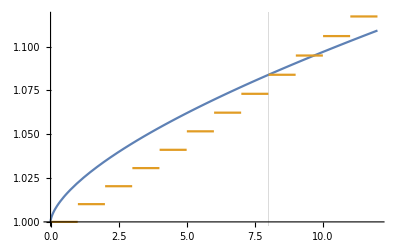

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.05], 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 12}, GridLines->{{8}}]
```

```mathematica
(* Perfect. Interpretation is correct. *)
```

```mathematica
(* Then product of price bracket and compound factor is playing catch up for the first 8 hours in order to get to point where decreasing over time? *)
```

```mathematica
(* Look at different price bracket VaR growth over time without compound factor *)
```

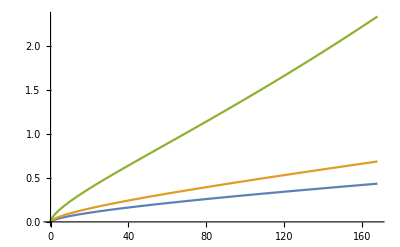

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.10] - 1), (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1), (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)}, {t, 0, 24*7}]
```

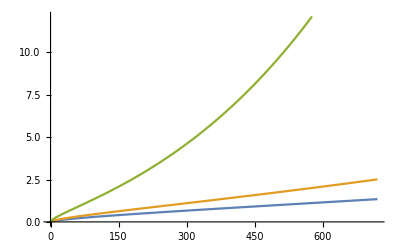

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.10] - 1), (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1), (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)}, {t, 0, 24*30}]
```

```mathematica
(* Try product of price bracket and compound factor for different anchor times in k calibration ... *)
```

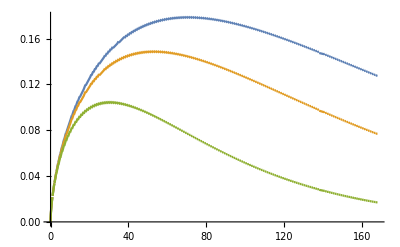

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

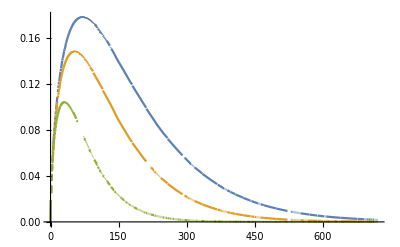

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc90dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

```mathematica
(* So most VaR to passive holders happens over shorter term when imbalance first created. Longer users hold positions and imbalance gets drawn down through funding, the more VaR gets curbed and eventually brought to zero *)
```

```mathematica
(* What if we underestimate funding rate needed? As in should have used alpha=0.01 instead of alpha=0.05? what does this do to VaR over time? *)
```

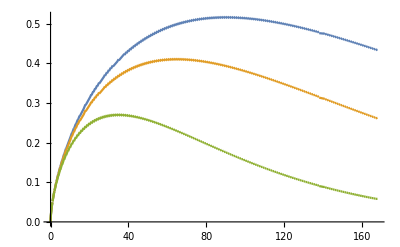

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

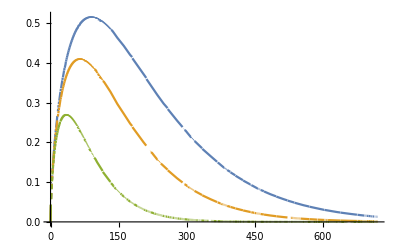

```mathematica
Plot[{(factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc90dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

```mathematica
(* Look at 1/compoundFactor (larger alpha than required) vs price factor BEFORE hit the anchor to see what new anchor time is ... *)
```

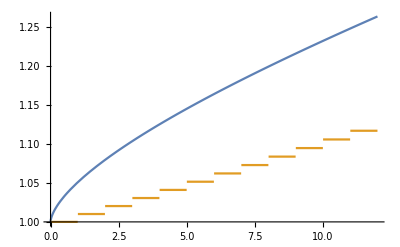

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 12}]
```

```mathematica
(* Interesting, anchor time comes much later. Not great, but still exists ... However, VaR still seems to decrease tho, just more drawn out AND significantly higher max value/peak (about 2x for alpha=0.05). *)
```

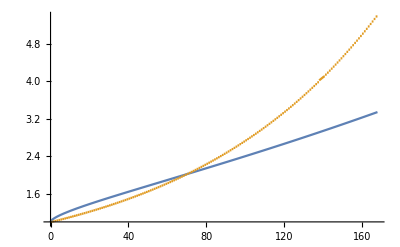

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

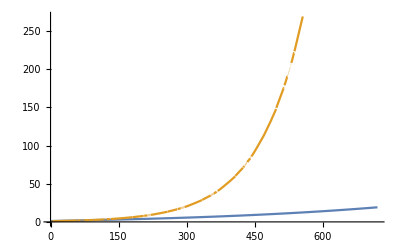

```mathematica
Plot[{factorWethUsdc90dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc90dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* Instead of anticipated anchor of 8h, get anchor around 72h (3d). *)
```

```mathematica
(* What about set funding factor to not exp^{(m*t)^{1/a}} but exp^{m*(t)^(1/a)}? What's difference in interest rate? *)
```

```mathematica
(* What about underestimating the stable distribution fit params? *)
```